```mathematica
α=1
ρ=.
```

1

```mathematica
ie[l_,ϵ_]:=BesselI[l,2*ϵ]
ke[l_,ϵ_]:=BesselK[l,2*ϵ]
i0[l_,ϵ_]:=BesselI[l,2*ϵ*Sqrt[ρ]]
k0[l_,ϵ_]:=BesselK[l,2*ϵ*Sqrt[ρ]]
```

```mathematica
ie[l,ϵ]
```

BesselI[l,2 ϵ]

```mathematica
Subscript[x, 0][ϵ_]:=(2*α)/(ϵ*ρ)*k0[1,ϵ]/(i0[1,ϵ]*(k0[0,ϵ]+k0[2,ϵ])+k0[1,ϵ]*(i0[0,ϵ]+i0[2,ϵ]))
Subscript[x, 1][ϵ_]:=(6*α)/(ϵ*ρ)*k0[3, ϵ]/(i0[3,ϵ]*(k0[2,ϵ]+k0[4,ϵ])+k0[3,ϵ]*(i0[2,ϵ]+i0[4,ϵ]))
Subscript[y, 0][ϵ_]:=-Subscript[x, 0][ϵ]*(ie[1,ϵ]-ϵ*(ie[0,ϵ]+ie[2,ϵ]))/(ke[1,ϵ]+ϵ*(ke[0,ϵ]+ke[2,ϵ]))
Subscript[y, 1][ϵ_]:=-Subscript[x, 1][ϵ]*(ie[3,ϵ]-ϵ*(ie[2,ϵ]+ie[4,ϵ]))/(ke[3,ϵ]+ϵ*(ke[2,ϵ]+ke[4,ϵ]))
```

```mathematica
FullForm[Subscript[x, 0][ϵ]]
```

```mathematica
snr[ϵ_]:=(Subscript[x, 1][ϵ]*ie[3,ϵ]+Subscript[y, 1][ϵ]*ke[3,ϵ])/Sqrt[Subscript[x, 0][ϵ]*ie[1,ϵ]+Subscript[y, 0][ϵ]*ke[1,ϵ]]
```

```mathematica
snr[0.45]
```

0.220584

```mathematica
Dsnr[ϵ_]=D[snr[ϵ],ϵ]
```

-(((-((2 BesselI[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ϵ^2 ρ ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ]))))+(2 (BesselI[0,2 ϵ]+BesselI[2,2 ϵ]) BesselK[1,2 ϵ √ρ])/(ϵ ρ ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))+(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ϵ^2 ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))+(2 (3 BesselI[1,2 ϵ]+BesselI[3,2 ϵ]) BesselK[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))-(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ √ρ] (-BesselK[0,2 ϵ]-BesselK[2,2 ϵ]))/(ϵ ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))+(2 BesselI[1,2 ϵ] (-BesselK[0,2 ϵ √ρ]-BesselK[2,2 ϵ √ρ]))/(ϵ √ρ ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))-(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ] (-BesselK[0,2 ϵ √ρ]-BesselK[2,2 ϵ √ρ]))/(ϵ √ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))+(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ] BesselK[1,2 ϵ √ρ] (-3 BesselK[1,2 ϵ]-BesselK[3,2 ϵ]))/(ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ]))^2 ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))-(2 BesselI[1,2 ϵ] BesselK[1,2 ϵ √ρ] ((2 √ρ BesselI[1,2 ϵ √ρ]+√ρ (BesselI[1,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ])) BesselK[1,2 ϵ √ρ]+√ρ (BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) (-BesselK[0,2 ϵ √ρ]-BesselK[2,2 ϵ √ρ])+√ρ (BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])+BesselI[1,2 ϵ √ρ] (-2 √ρ BesselK[1,2 ϵ √ρ]+√ρ (-BesselK[1,2 ϵ √ρ]-BesselK[3,2 ϵ √ρ]))))/(ϵ ρ ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ]))^2)+(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ] BesselK[1,2 ϵ √ρ] ((2 √ρ BesselI[1,2 ϵ √ρ]+√ρ (BesselI[1,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ])) BesselK[1,2 ϵ √ρ]+√ρ (BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) (-BesselK[0,2 ϵ √ρ]-BesselK[2,2 ϵ √ρ])+√ρ (BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])+BesselI[1,2 ϵ √ρ] (-2 √ρ BesselK[1,2 ϵ √ρ]+√ρ (-BesselK[1,2 ϵ √ρ]-BesselK[3,2 ϵ √ρ]))))/(ϵ ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ]))^2)) ((6 BesselI[3,2 ϵ] BesselK[3,2 ϵ √ρ])/(ϵ ρ ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))-(6 (BesselI[3,2 ϵ]-ϵ (BesselI[2,2 ϵ]+BesselI[4,2 ϵ])) BesselK[3,2 ϵ] BesselK[3,2 ϵ √ρ])/(ϵ ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ])) ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))))/(2 ((2 BesselI[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ϵ ρ ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))-(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ϵ ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ]))))^(3/2)))+(-((6 BesselI[3,2 ϵ] BesselK[3,2 ϵ √ρ])/(ϵ^2 ρ ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ]))))+(6 (BesselI[2,2 ϵ]+BesselI[4,2 ϵ]) BesselK[3,2 ϵ √ρ])/(ϵ ρ ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))+(6 (BesselI[3,2 ϵ]-ϵ (BesselI[2,2 ϵ]+BesselI[4,2 ϵ])) BesselK[3,2 ϵ] BesselK[3,2 ϵ √ρ])/(ϵ^2 ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ])) ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))+(6 (BesselI[1,2 ϵ]+2 BesselI[3,2 ϵ]+BesselI[5,2 ϵ]) BesselK[3,2 ϵ] BesselK[3,2 ϵ √ρ])/(ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ])) ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))-(6 (BesselI[3,2 ϵ]-ϵ (BesselI[2,2 ϵ]+BesselI[4,2 ϵ])) BesselK[3,2 ϵ √ρ] (-BesselK[2,2 ϵ]-BesselK[4,2 ϵ]))/(ϵ ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ])) ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))+(6 BesselI[3,2 ϵ] (-BesselK[2,2 ϵ √ρ]-BesselK[4,2 ϵ √ρ]))/(ϵ √ρ ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))-(6 (BesselI[3,2 ϵ]-ϵ (BesselI[2,2 ϵ]+BesselI[4,2 ϵ])) BesselK[3,2 ϵ] (-BesselK[2,2 ϵ √ρ]-BesselK[4,2 ϵ √ρ]))/(ϵ √ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ])) ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))+(6 (BesselI[3,2 ϵ]-ϵ (BesselI[2,2 ϵ]+BesselI[4,2 ϵ])) BesselK[3,2 ϵ] BesselK[3,2 ϵ √ρ] (-BesselK[1,2 ϵ]-2 BesselK[3,2 ϵ]-BesselK[5,2 ϵ]))/(ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ]))^2 ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])))-(6 BesselI[3,2 ϵ] BesselK[3,2 ϵ √ρ] ((√ρ (BesselI[1,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ])+√ρ (BesselI[3,2 ϵ √ρ]+BesselI[5,2 ϵ √ρ])) BesselK[3,2 ϵ √ρ]+√ρ (BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) (-BesselK[2,2 ϵ √ρ]-BesselK[4,2 ϵ √ρ])+√ρ (BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])+BesselI[3,2 ϵ √ρ] (√ρ (-BesselK[1,2 ϵ √ρ]-BesselK[3,2 ϵ √ρ])+√ρ (-BesselK[3,2 ϵ √ρ]-BesselK[5,2 ϵ √ρ]))))/(ϵ ρ ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ]))^2)+(6 (BesselI[3,2 ϵ]-ϵ (BesselI[2,2 ϵ]+BesselI[4,2 ϵ])) BesselK[3,2 ϵ] BesselK[3,2 ϵ √ρ] ((√ρ (BesselI[1,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ])+√ρ (BesselI[3,2 ϵ √ρ]+BesselI[5,2 ϵ √ρ])) BesselK[3,2 ϵ √ρ]+√ρ (BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) (-BesselK[2,2 ϵ √ρ]-BesselK[4,2 ϵ √ρ])+√ρ (BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ])+BesselI[3,2 ϵ √ρ] (√ρ (-BesselK[1,2 ϵ √ρ]-BesselK[3,2 ϵ √ρ])+√ρ (-BesselK[3,2 ϵ √ρ]-BesselK[5,2 ϵ √ρ]))))/(ϵ ρ (BesselK[3,2 ϵ]+ϵ (BesselK[2,2 ϵ]+BesselK[4,2 ϵ])) ((BesselI[2,2 ϵ √ρ]+BesselI[4,2 ϵ √ρ]) BesselK[3,2 ϵ √ρ]+BesselI[3,2 ϵ √ρ] (BesselK[2,2 ϵ √ρ]+BesselK[4,2 ϵ √ρ]))^2))/(√((2 BesselI[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ϵ ρ ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))-(2 (BesselI[1,2 ϵ]-ϵ (BesselI[0,2 ϵ]+BesselI[2,2 ϵ])) BesselK[1,2 ϵ] BesselK[1,2 ϵ √ρ])/(ϵ ρ (BesselK[1,2 ϵ]+ϵ (BesselK[0,2 ϵ]+BesselK[2,2 ϵ])) ((BesselI[0,2 ϵ √ρ]+BesselI[2,2 ϵ √ρ]) BesselK[1,2 ϵ √ρ]+BesselI[1,2 ϵ √ρ] (BesselK[0,2 ϵ √ρ]+BesselK[2,2 ϵ √ρ])))))

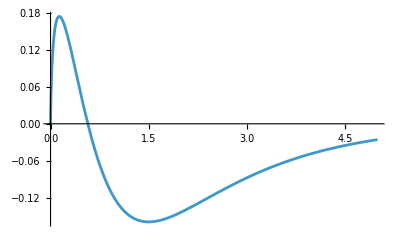

```mathematica
Plot[Dsnr[ϵ],{ϵ,0,5}]
```

```mathematica
FindRoot[Dsnr[ϵ],{ϵ,0.5}]
```

{ϵ→0.570474}